```mathematica
Pi2=-4 al/Pi(5/18-3/18Log[m^2/me^2]-0.03002)
```

-(4 al (0.247758-1/6 Log[m^2/me^2]))/π

```mathematica
c1=Pi2/.m->105.658/.me->0.511/.al->1/137
Pi2 Pi/al/.m->105.658/.me->0.511/.al->1/137
```

0.0142142

6.11776

```mathematica
P="+[Logme]*(-8896/75*m^-4+512/5*m^-4*[LogD]-512/5*m^-4*[Logm])-81248/225*m^-4+32/5*m^-4*nn7-32/5*m^-4*nn6-288/5*m^-4*nn5+32/5*m^-4*nn4+512/5*m^-4*[LogD]+18496/75*m^-4*[Log2]-512/5*m^-4*[Log2]*[LogD]+1216/75*m^-4*[Logm]-512/5*m^-4*[Logm]*[LogD]+512/5*m^-4*[Logm]*[Log2]+512/5*m^-4*[Logm]^2+64/15*m^-4*Pi^2"
```

+[Logme]*(-8896/75*m^-4+512/5*m^-4*[LogD]-512/5*m^-4*[Logm])-81248/225*m^-4+32/5*m^-4*nn7-32/5*m^-4*nn6-288/5*m^-4*nn5+32/5*m^-4*nn4+512/5*m^-4*[LogD]+18496/75*m^-4*[Log2]-512/5*m^-4*[Log2]*[LogD]+1216/75*m^-4*[Logm]-512/5*m^-4*[Logm]*[LogD]+512/5*m^-4*[Logm]*[Log2]+512/5*m^-4*[Logm]^2+64/15*m^-4*Pi^2

```mathematica
Pfro=ToExpression[StringReplace[P,{"[Log2]"->"Log[2]","[Logme]"->"Log[me]","[LogD]"->"Log[d]","[Logm]"->"Log[m]"}]]

Pp="[Logme]*(-8896/75*m^-4+512/5*m^-4*[LogD]-512/5*m^-4*[Logm])-6112/25*m^-4+256/5*m^-4*nn12+128/15*m^-4*nn11+128/5*m^-4*nn10+128/5*m^-4*nn3+512/5*m^-4*[LogD]+18496/75*m^-4*[Log2]-512/5*m^-4*[Log2]*[LogD]+1216/75*m^-4*[Logm]-512/5*m^-4*[Logm]*[LogD]+512/5*m^-4*[Logm]*[Log2]+512/5*m^-4*[Logm]^2+64/15*m^-4*Pi^2"
Pfrp=ToExpression[StringReplace[Pp,{"[Log2]"->"Log[2]","[Logme]"->"Log[me]","[LogD]"->"Log[d]","[Logm]"->"Log[m]"}]]
```

-81248/(225 m^4)+(32 nn4)/(5 m^4)-(288 nn5)/(5 m^4)-(32 nn6)/(5 m^4)+(32 nn7)/(5 m^4)+(64 π^2)/(15 m^4)+(18496 Log[2])/(75 m^4)+(512 Log[d])/(5 m^4)-(512 Log[2] Log[d])/(5 m^4)+(1216 Log[m])/(75 m^4)+(512 Log[2] Log[m])/(5 m^4)-(512 Log[d] Log[m])/(5 m^4)+(512 Log[m]^2)/(5 m^4)+(-8896/(75 m^4)+(512 Log[d])/(5 m^4)-(512 Log[m])/(5 m^4)) Log[me]

[Logme]*(-8896/75*m^-4+512/5*m^-4*[LogD]-512/5*m^-4*[Logm])-6112/25*m^-4+256/5*m^-4*nn12+128/15*m^-4*nn11+128/5*m^-4*nn10+128/5*m^-4*nn3+512/5*m^-4*[LogD]+18496/75*m^-4*[Log2]-512/5*m^-4*[Log2]*[LogD]+1216/75*m^-4*[Logm]-512/5*m^-4*[Logm]*[LogD]+512/5*m^-4*[Logm]*[Log2]+512/5*m^-4*[Logm]^2+64/15*m^-4*Pi^2

-6112/(25 m^4)+(128 nn10)/(5 m^4)+(128 nn11)/(15 m^4)+(256 nn12)/(5 m^4)+(128 nn3)/(5 m^4)+(64 π^2)/(15 m^4)+(18496 Log[2])/(75 m^4)+(512 Log[d])/(5 m^4)-(512 Log[2] Log[d])/(5 m^4)+(1216 Log[m])/(75 m^4)+(512 Log[2] Log[m])/(5 m^4)-(512 Log[d] Log[m])/(5 m^4)+(512 Log[m]^2)/(5 m^4)+(-8896/(75 m^4)+(512 Log[d])/(5 m^4)-(512 Log[m])/(5 m^4)) Log[me]

```mathematica
c2=-5/64Pfro*m^4al/(4Pi)/.m->105.658/.me->0.511/.al->1/137//Simplify
c2p=-5/64 Pfrp*m^4 al/(4 Pi)/.m->105.7/.me->0.511/.al->1/137//Chop//Simplify
cpnonlog=-5/64 Pfrp*m^4 al/(4 Pi)/.m->1/.me->1/.al->1/137//Chop//Simplify
Pi2/.m->1/.me->1/.al->1/137
```

-0.130792-0.000290429 nn4+0.00261386 nn5+0.000290429 nn6-0.000290429 nn7+0.0233493 Log[d]

-0.136104-0.00116171 nn10-0.000387238 nn11-0.00232343 nn12-0.00116171 nn3+0.0233511 Log[d]

-1/(16440 π)(-573+60 nn10+20 nn11+120 nn12+60 nn3+10 π^2+578 Log[2]-240 (-1+Log[2]) Log[d])

-0.00230259

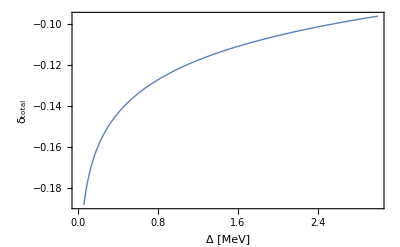

```mathematica
Plot[c2+c1,{d,0,3},Frame->True,FrameLabel->{"Δ  [MeV]",Subscript[δ,total]},PlotStyle->Thick]
```

```mathematica
c2
```

-0.130792-0.000290429 nn4+0.00261386 nn5+0.000290429 nn6-0.000290429 nn7+0.0233493 Log[d]

```mathematica
Export["~/plot1.eps",Plot[c2+c1,{d,0,3},Frame->True,FrameLabel->{"Δ  [MeV]",Subscript[δ,total]},PlotStyle->Thick]]
```

~/plot1.eps

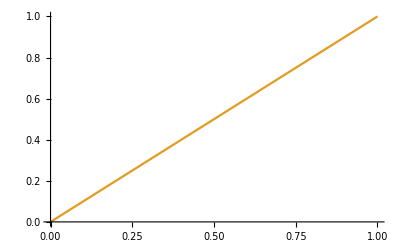

```mathematica
Plot[{((1+(c2+c1))d^5)^(1/5),d},{d,0,1}]
```

```mathematica
Integrate[(1+(c2+c1)) d^5,{d,0,1}]/Integrate[ d^5,{d,0,1}]
```

1.15484

```mathematica
-32*m^-4*b^2+128/5*m^-4*a*b-32/5*m^-4*a^2/.a->1/.b->1
```

-64/(5 m^4)

```mathematica
Coefficient[-5/64 Pfro*m^4 /(4 ),Log[m]]//Simplify
Coefficient[-5/64 Pfro*m^4/(4),Log[d]]//Simplify
```

-19/60-Log[4]+2 Log[d]+2 Log[me]

2 (-1+Log[(2 m)/me])

```mathematica
-5/64 Pfro*m^4/(4)//Expand
```

0.533771-2 Log[d]+2 Log[2] Log[d]-(19 Log[m])/60-2 Log[2] Log[m]+2 Log[d] Log[m]-2 Log[m]^2+(139 Log[me])/60-2 Log[d] Log[me]+2 Log[m] Log[me]

```mathematica
FullSimplify[-2 Log[d]+2 Log[2] Log[d]-(19 Log[m])/60-2 Log[2] Log[m]+2 Log[d] Log[m]-2 Log[m]^2+(139 Log[me])/60-2 Log[d] Log[me]+2 Log[m] Log[me]]
```

```mathematica
2 Log[d] (-1+Log[(2 m)/me])+(139 Log[me])/60+Log[m] (-19/60+Log[me^2/(4 m^2)])/.Log[(2 m)/me]->x/.Log[me^2/(4 m^2)]->-2x//Expand
```

-2 Log[d]+2 x Log[d]-(19 Log[m])/60-2 x Log[m]+(139 Log[me])/60

```mathematica
2x Log[d/m]+2Log[me/d]+19/60 Log[me/m]
```

```mathematica
2 Log[(2 m)/me] Log[d/m]+2 Log[me/d]+19/60 Log[me/m]
```

```mathematica
2 Log[d/m] Log[(2 m)/me]+2 Log[me/d]+19/60 Log[me/m]+0.533771/.me->1232/.d->1232323//Simplify
-5/64 Pfro*m^4/(4)/.me->1232/.d->1232323//Simplify
```

-191.193+40.5787 Log[m]-2. Log[m]^2

-191.193+40.5787 Log[m]-2. Log[m]^2

```mathematica
2 Log[d/m] Log[(2 m)/me]+2 Log[me/d]+19/60 Log[me/m]+0.533771//TeXForm
```

2 \log \left(\frac{d}{m}\right) \log
   \left(\frac{2 m}{\text{me}}\right)+2
   \log
   \left(\frac{\text{me}}{d}\right)+\frac{
   19}{60} \log
   \left(\frac{\text{me}}{m}\right)+0.5337
   71

```mathematica
FullSimplify[-2 Log[d]+2 Log[2] Log[d]+(139 Log[me])/60-2 Log[d] Log[me]-19/60 Log[me x]-2 Log[2] Log[me x]+2 Log[d] Log[me x]+2 Log[me] Log[me x]-2 Log[me x]^2,x>0&&me>0&&d>0]
```

-(19 Log[x])/60+2 (-Log[d]+Log[me]+Log[2 x] (Log[d]-Log[me x]))

```mathematica
s1=Series[(m-d)^(1-ep),{d,0,5},{ep,0,5}];
s2=Series[(m-d)^(1-ep),{ep,0,5},{d,0,5}];
```

```mathematica
s1-s2//Normal//Simplify
```

0

```mathematica
Integrate[d^5(a+b Log[d]),{d,0,dc}]
```

1/36 dc^6 (6 a-b+6 b Log[dc])

```mathematica
Fermi[r_,a_,r0_]:=1/(1+Exp[(r-r0)/a])/(a Log[1+E^(r0/a)])
```

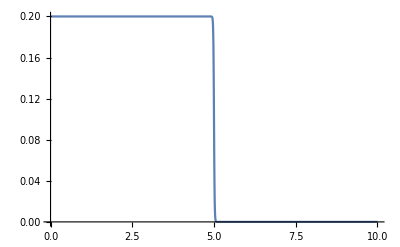

```mathematica
Plot[Fermi[r,1/100,5],{r,0,10}]
```